triangle with an almost recangular angle at y_p

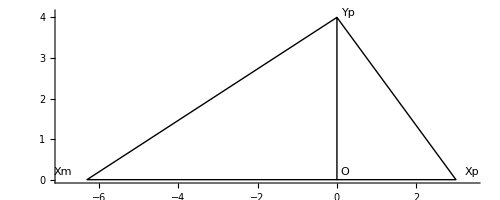

```mathematica
xp=3;yp=4;xm=-6.3;Show[Graphics[
Line[{{0,0},{xp,0},{0,yp},{0,0},{xm,0},{0,yp}}],Axes->True],
Graphics[Text["Xp",{xp+0.4,0.2}]],
Graphics[Text["Yp",{0.3,yp+0.1}]],
Graphics[Text["Xm",{xm-0.6,0.2}]],
Graphics[Text["O",{0.2,0.2}]]]
```

trivial rotation of the 3-4-5-triangle around the y-axis

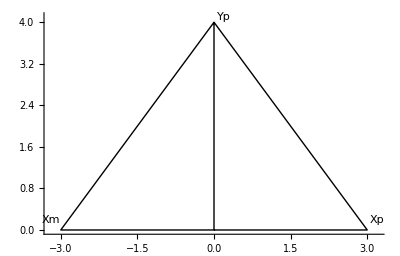

```mathematica
xp=3;yp=4;xm=-3;Show[
Graphics[Line[{{0,0},{xp,0},{0,yp},{0,0},{xm,0},{0,yp}}],Axes->True],
Graphics[Text["Xp",{xp+0.2,0.2}]],
Graphics[Text["Yp",{0.2,yp+0.1}]],
Graphics[Text["Xm",{xm-0.2,0.2}]]]
```

trivial rotation of the 3-4-5 triangle around x- and y-axis, giving a rhombus

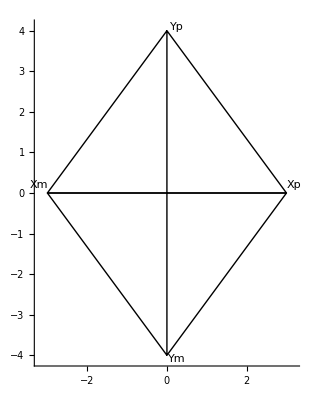

```mathematica
xp=3;yp=4;xm=-3;ym=-4;Show[
Graphics[Line[{{0,0},{xp,0},{0,yp},{0,0},{xm,0},{0,yp}}],Axes->True],
Graphics[Line[{{0,0},{xp,0},{0,ym},{0,0},{xm,0},{0,ym}}],Axes->True],
Graphics[Text["Xp",{xp+0.2,0.2}]],
Graphics[Text["Yp",{0.25,yp+0.1}]],
Graphics[Text["Xm",{xm-0.2,0.2}]],
Graphics[Text["Ym",{0.25,ym-0.1}]]]
```

trivial rotation of 3-rectangular polyhedron with 3 3-4-5-pythagorean triangles a it sides around x-, y- and z-axis, giving octahedron of 8 3-rectangular tetrahedrons. 
Colors:  blue x-y-plane, green y-z-plane, red x-z plane
The enclosing cube is drawn by Mathematics. The enclosed cube can be obtained by connecting midpoints of the 12 sides.

```mathematica
xp=3;yp=4;xm=-3;ym=-4;zp=3;zm=-3;Show[
Graphics3D[{Directive[Dashed,Blue],Line[{{xp,0,0},{xm,0,0}}],Axes->True}],
Graphics3D[{Directive[Dashed,Green],Line[{{0,yp,0},{0,ym,0}}],Axes->True}],
Graphics3D[{Directive[Dashed,Red],Line[{{0,0,zp},{0,0,zm}}],Axes->True}],
Graphics3D[{Directive[Thick,Blue   ],Line[{{xm,0,0},{0,ym,0},{xp,0,0},{0,yp,0},{xm,0,0}}],Axes->True}],
Graphics3D[{Directive[Thick,Green],Line[{{0,ym,0},{0,0,zm},{0,yp,0},{0,0,zp},{0,ym,0}}],Axes->True}],
Graphics3D[{Directive[Thick,Red],     Line[{{0,0,zm},{xm,0,0},{0,0,zp},{xp,0,0},{0,0,zm}}],Axes->True}],
Graphics3D[Text["Xp",{xp+0.2,0.2,0}]],
Graphics3D[Text["Yp",{0.25,yp+0.1,0}]],
Graphics3D[Text["Xm",{xm-0.2,0.2,0}]],
Graphics3D[Text["Ym",{0.25,ym-0.1,0}]],
Graphics3D[Text["Zp",{0.25,0.2,zp+0.1}]],
Graphics3D[Text["Zm",{0.25,0.2,zm-0.1}]]
]
```

-Graphics3D-

```mathematica
xp=3;yp=4;xm=-3;ym=-4;zp=3;zm=-3;Show[
Graphics3D[Line[{{xp,0,0},{0,ym,0}}],Axes->True],
Graphics3D[Line[{{0,yp,0},{0,0,zm}}],Axes->True],
Graphics3D[Line[{{0,0,zp},{xm,0,0}}],Axes->True],
Graphics3D[{Directive[Thick,Blue   ],Line[{{xm,0,0},{0,ym,0},{xp,0,0},{0,yp,0},{xm,0,0}}],Axes->True}],
Graphics3D[{Directive[Thick,Green],Line[{{0,ym,0},{0,0,zm},{0,yp,0},{0,0,zp},{0,ym,0}}],Axes->True}],
Graphics3D[{Directive[Thick,Red],     Line[{{0,0,zm},{xm,0,0},{0,0,zp},{xp,0,0},{0,0,zm}}],Axes->True}],
Graphics3D[Text["Xp",{xp+0.2,0.2,0}]],
Graphics3D[Text["Yp",{0.25,yp+0.1,0}]],
Graphics3D[Text["Xm",{xm-0.2,0.2,0}]],
Graphics3D[Text["Ym",{0.25,ym-0.1,0}]],
Graphics3D[Text["Zp",{0.25,0.2,zp+0.1}]],
Graphics3D[Text["Zm",{0.25,0.2,zm-0.1}]]
]
```

-Graphics3D-